-Graphics-

```mathematica
Remove["`*"]
```

-Graphics-

```mathematica
ϵ=1/2(Grad[{u[t,x,y],v[t,x,y]},{x,y}]+Grad[{u[t,x,y],v[t,x,y]},{x,y}]ᵀ);
```

```mathematica
σ=λ Div[{u[t,x,y],v[t,x,y]},{x,y}]IdentityMatrix[2]+2μ ϵ
```

{{2 μ u^(0,1,0)[t,x,y]+λ (v^(0,0,1)[t,x,y]+u^(0,1,0)[t,x,y]),μ (u^(0,0,1)[t,x,y]+v^(0,1,0)[t,x,y])},{μ (u^(0,0,1)[t,x,y]+v^(0,1,0)[t,x,y]),2 μ v^(0,0,1)[t,x,y]+λ (v^(0,0,1)[t,x,y]+u^(0,1,0)[t,x,y])}}

```mathematica
TraditionalForm[σ]
```

(λ (u^(0,1,0)(t,x,y)+v^(0,0,1)(t,x,y))+2 μ u^(0,1,0)(t,x,y) | μ (u^(0,0,1)(t,x,y)+v^(0,1,0)(t,x,y))
μ (u^(0,0,1)(t,x,y)+v^(0,1,0)(t,x,y)) | λ (u^(0,1,0)(t,x,y)+v^(0,0,1)(t,x,y))+2 μ v^(0,0,1)(t,x,y))

-Graphics--Graphics-
第二个初值条件改成
-Graphics-

```mathematica
λ=1;μ=2;
```

```mathematica
f1[t_,x_,y_]:=π^2(λ+3μ-1)Sin[π t]Sin[π x]Sin[π y]-(2x-1)(2y-1)(λ+μ)Cos[t];
f2[t_,x_,y_]:=Cos[t](2μ(-2(x-1)x-y^2+y)-(x-1)x(2λ+(y-1)y))-π^2(λ+μ)Sin[π t]Cos[π x]Cos[π y]
```

```mathematica
pde=D[{u[t,x,y],v[t,x,y]},{t,2}]-Div[σ,{x,y}]=={f1[t,x,y],f2[t,x,y]};
```

```mathematica
ics={u[0,x,y]==0,v[0,x,y]==(-1+x) x (-1+y) y,Derivative[1,0,0][u][0,x,y]==π Sin[π x]Sin[π y],Derivative[1,0,0][v][0,x,y]==0};(*初值条件*)
```

```mathematica
bcs={DirichletCondition[{u[t,x,y]==0,v[t,x,y]==2(y-1)y Cos[t]},x==-1],DirichletCondition[{u[t,x,y]==0,v[t,x,y]==0},x==1],DirichletCondition[{u[t,x,y]==0,v[t,x,y]==2(x-1)x Cos[t]},y==-1],DirichletCondition[{u[t,x,y]==0,v[t,x,y]==0},y==1]};(*边界条件*)
```

```mathematica
sol=NDSolve[{pde,bcs,ics},{u,v},{t,0,1},{x,-1,1},{y,-1,1}]
```

{{u→InterpolatingFunction[{{0., 1.}, {-1., 1.}, {-1., 1.}}, <>],v→InterpolatingFunction[{{0., 1.}, {-1., 1.}, {-1., 1.}}, <>]}}

```mathematica
Plot3D[u[1,x,y]/.sol,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[v[1,x,y]/.sol,{x,-1,1},{y,-1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Block[{solu=u[t,x,y]/.sol,solv=v[t,x,y]/.sol},pics=Table[{ContourPlot[solu,{x,-1,1},{y,-1,1}],ContourPlot[solv,{x,-1,1},{y,-1,1}]},{t,0,1,0.1}]];
```

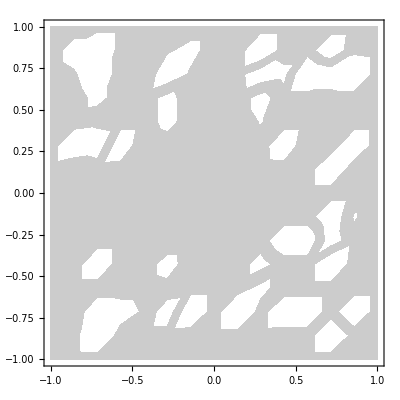
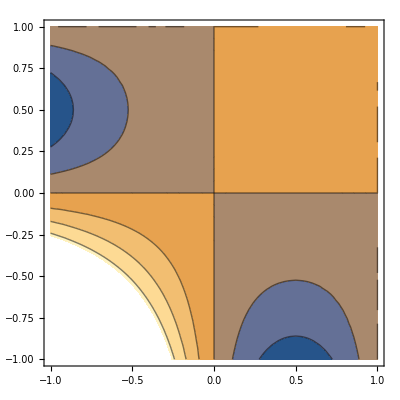

```mathematica
pics[[1]]
```

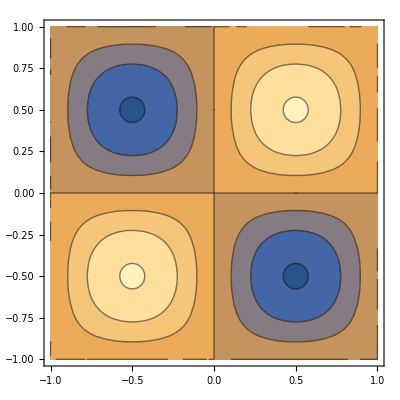
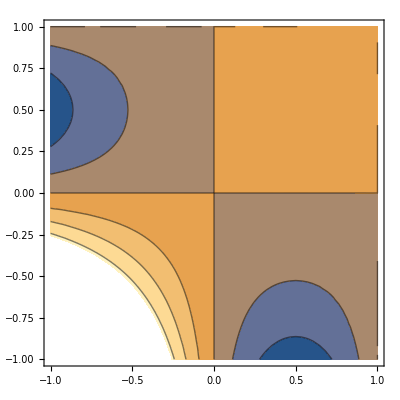

```mathematica
pics[[2]]
```

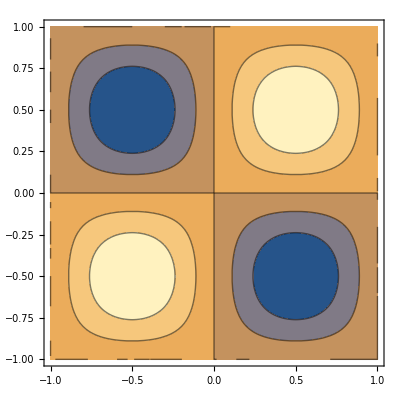
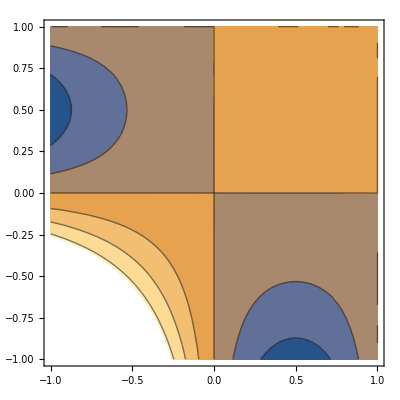

```mathematica
pics[[3]]
```

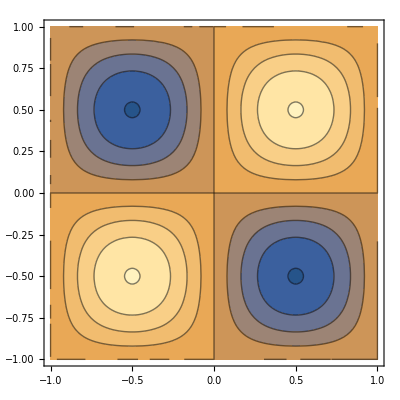
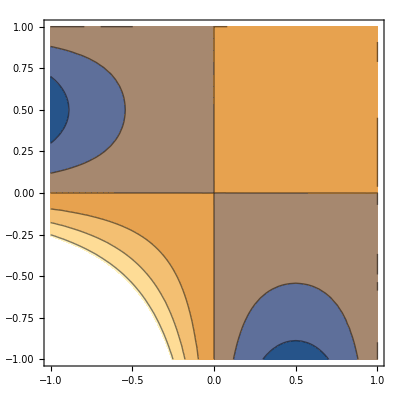

```mathematica
pics[[4]]
```

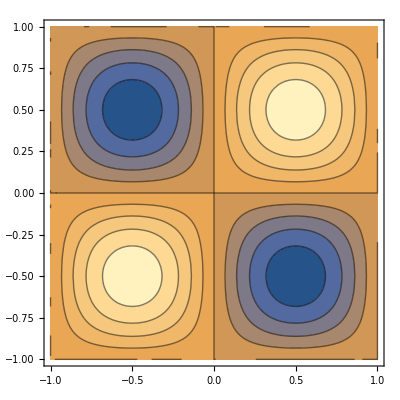
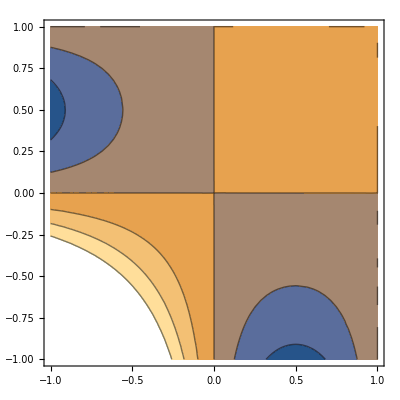

```mathematica
pics[[5]]
```

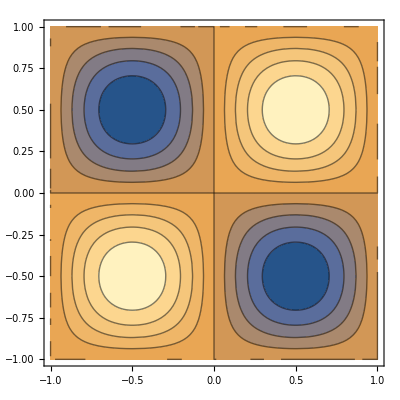
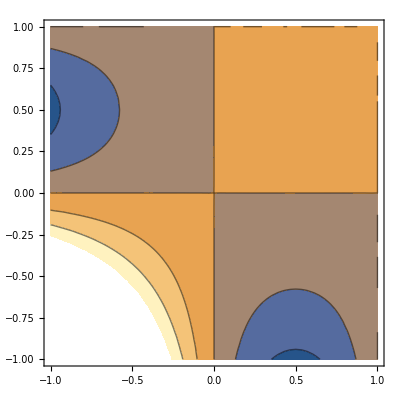

```mathematica
pics[[6]]
```

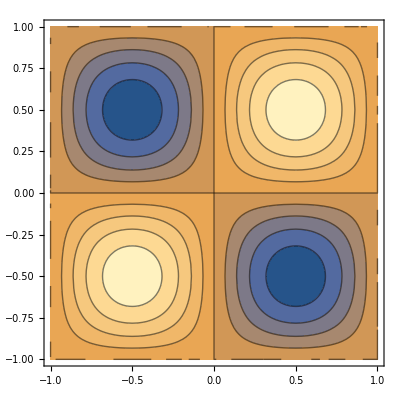
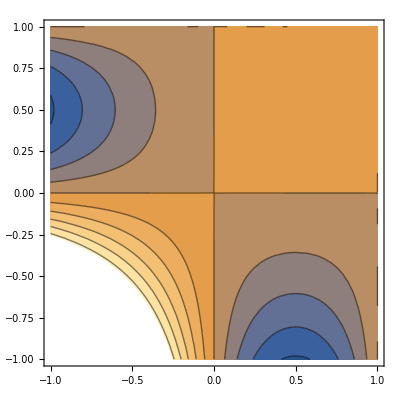

```mathematica
pics[[7]]
```

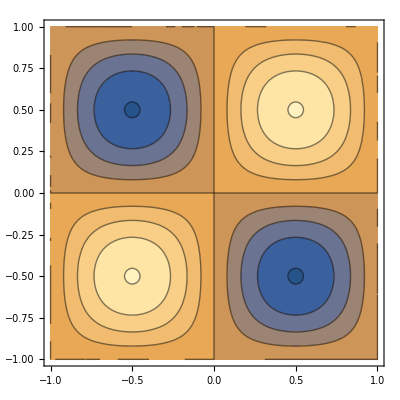
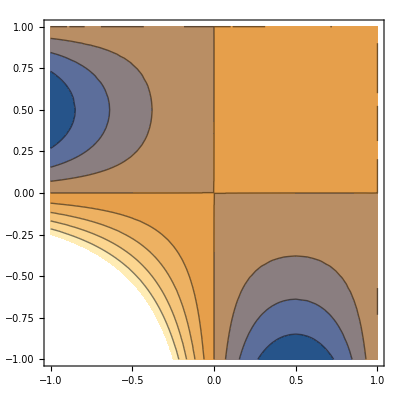

```mathematica
pics[[8]]
```

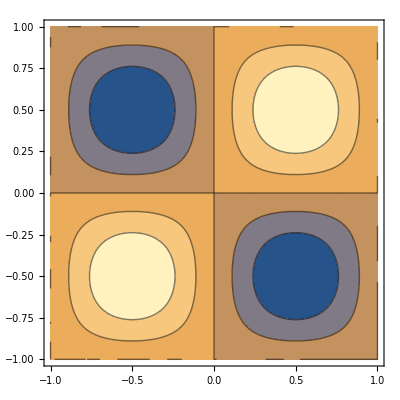
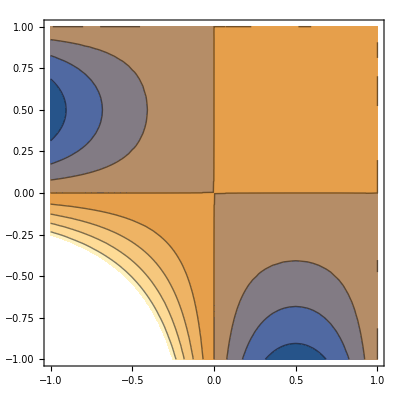

```mathematica
pics[[9]]
```

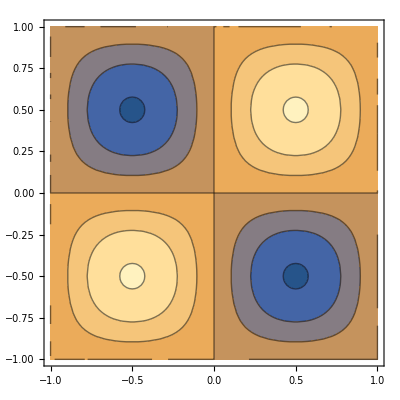
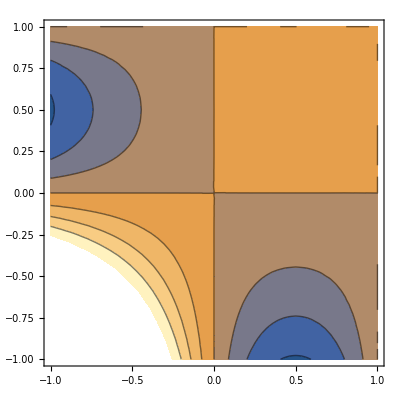

```mathematica
pics[[10]](*t=0.9s*)
```

```mathematica
uExact[t_,x_,y_]:=Sin[π x]Sin[π y]Sin[π t];
vExact[t_,x_,y_]:=x(x-1)y(y-1)Cos[t];
```

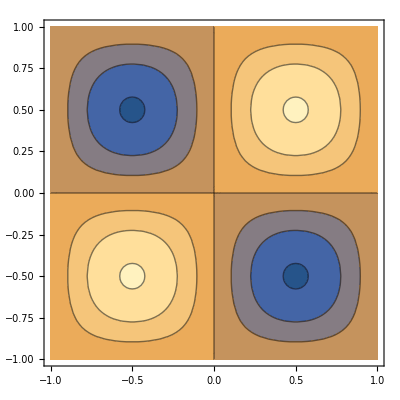

```mathematica
ContourPlot[uExact[0.9,x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
pde/.{u->uExact,v->vExact}//Simplify
```

True

```mathematica
pde[[1]]//.Flatten@{sol,t->0,x->0,y->0}
```

{-2.97,-0.116663}

```mathematica
pde[[2]]//.Flatten@{sol,t->0,x->0,y->0}
```

{-3,0}

```mathematica
pde[[1]]//.Flatten@{sol,t->0.2,x->0,y->0}
```

{-2.91222,-17.6908}

```mathematica
pde[[2]]//.Flatten@{sol,t->0.2,x->0,y->0}
```

{-2.9402,-17.4036}

验证解析解的边界条件:

```mathematica
bcs
```

{DirichletCondition[{u[t,x,y]==0,v[t,x,y]==2 (-1+y) y Cos[t]},x==-1],DirichletCondition[{u[t,x,y]==0,v[t,x,y]==0},x==1],DirichletCondition[{u[t,x,y]==0,v[t,x,y]==2 (-1+x) x Cos[t]},y==-1],DirichletCondition[{u[t,x,y]==0,v[t,x,y]==0},y==1]}

```mathematica
bcs/.{u->uExact,v->vExact}
```

{DirichletCondition[{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-1+y) y Cos[t]==2 (-1+y) y Cos[t]},x==-1],DirichletCondition[{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-1+y) y Cos[t]==0},x==1],DirichletCondition[{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-1+y) y Cos[t]==2 (-1+x) x Cos[t]},y==-1],DirichletCondition[{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-1+y) y Cos[t]==0},y==1]}

```mathematica
Cases[bcs,DirichletCondition[x_,y_]:>{x,ToRules[y]}]
```

{{{u[t,x,y]==0,v[t,x,y]==2 (-1+y) y Cos[t]},{x→-1}},{{u[t,x,y]==0,v[t,x,y]==0},{x→1}},{{u[t,x,y]==0,v[t,x,y]==2 (-1+x) x Cos[t]},{y→-1}},{{u[t,x,y]==0,v[t,x,y]==0},{y→1}}}

```mathematica
Simplify[%/.{u->uExact,v->vExact}]
```

{{{Sin[π t] Sin[π x] Sin[π y]==0,(-2-x+x^2) (-1+y) y Cos[t]==0},{x→-1}},{{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-1+y) y Cos[t]==0},{x→1}},{{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-2-y+y^2) Cos[t]==0},{y→-1}},{{Sin[π t] Sin[π x] Sin[π y]==0,(-1+x) x (-1+y) y Cos[t]==0},{y→1}}}

```mathematica
#1/.#2&@@@%
```

{{True,True},{True,True},{True,True},{True,True}}

```mathematica
Simplify[ics/.{u->uExact,v->vExact}]
```

{True,True,True,True}

验证解析解的初值条件:

```mathematica
ics[[2]]
```

v[0,x,y]==(-1+x) x (-1+y) y

```mathematica
vExact[0,x,y]
```

(-1+x) x (-1+y) y